```mathematica
Remove["Global`*"] (* Remove other names *)
```

# An Example of Training a Digit Classifier

## 一个简单的手写数字识别网络 LeNet 的笔记

author: 凉凉

参考 Wolfram U 中的课程 ["Introduction to Neural Networks"](https://www.wolfram.com/wolfram-u/courses/machine-learning/introduction-neural-networks-ml010/), 其中的训练手写数字识别的例子做的笔记. 其中关于 LeNet 网络的解释主要来源于 ["动手深度学习: LeNet"](https://zh.d2l.ai/chapter_convolutional-neural-networks/lenet.html). 但是没有对网络的解释, 只是机械地使用, 类似于过一遍如何使用 MMA 来操作神经网络的一个例子.

## 数据下载

```mathematica
trainingData=ResourceData["MNIST","TrainingData"];
testData=ResourceData["MNIST","TestData"];
```

```mathematica
RandomSample[trainingData,5]
```

{-Graphics-→5,-Graphics-→6,-Graphics-→2,-Graphics-→5,-Graphics-→9}

对于这样的数据, 通过 NetEncode 和 NetDecode 来处理网络中的输入和输出:

输出是根据输入图片得到的一个分类, 每个分类对应的数字大小范围为 0~9

```mathematica
dec=NetDecoder[{"Class",Range[0,9]}]
```

NetDecoder[<>]

将输入的图片以灰度形式规范为 28×28 的一个张量

```mathematica
enc=NetEncoder[{"Image",{28,28},"Grayscale"}]
```

NetEncoder[<>]

为了方便之后的训练, 将输入的数据转换为 Association 的形式:

```mathematica
trainAssoc=<|"Input"->Keys@trainingData,"Target"->Values@trainingData+1|>;
testAssoc=<|"Input"->Keys@testData,"Target"->Values@testData+1|>;
```

```mathematica
Take[trainAssoc,All,5]
```

<|Input→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Target→{1,1,1,1,1}|>

## 网络介绍

使用的是 ["LeNet (Wikipedia)"](https://en.wikipedia.org/wiki/LeNet) 的网络. 具体网络有什么用, 以及怎么构建这样的网络我不清楚, 可以去参考原始的论文: ["Gradient.02Based Learning Applied to Do cument Recognition"](http://vision.stanford.edu/cs598_spring07/papers/Lecun98.pdf).

图片来源: ["动手深度学习: LeNet"](https://zh.d2l.ai/chapter_convolutional-neural-networks/lenet.html#img-lenet)

```mathematica
uninitializedLenet=NetChain[{
ConvolutionLayer[20,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
ConvolutionLayer[50,5],
ElementwiseLayer[Ramp],
PoolingLayer[2,2],
LinearLayer[500],
ElementwiseLayer[Ramp],
LinearLayer[10],
SoftmaxLayer[]},
"Input"->enc,
"Output"->dec]
```

NetChain[<>]

然后构建一个用于学习的网络:

```mathematica
trainingNet=
NetInitialize@NetGraph[<|
"lenet"->uninitializedLenet,
"loss"->CrossEntropyLossLayer["Index"]|>,
{NetPort["Input"]->"lenet"->NetPort["loss","Input"],
NetPort["Target"]->NetPort["loss","Target"]}]
```

NetGraph[<>]

于是就构建了一个用来训练用的网络, 其大意如下: 输入经过 LeNet 后应该得到的是一个 0~9 (共 10 种) 的输出, 对于这个输出, 分别和目标 Target 去进行比较, 比较函数是 CrossEntropyLossLayer. 最终计算得到 Loss 即偏差值.

注: LeNet 的输出是 0~9 的数字, 但是经过索引 (Index) 后是以 1~10 去和 Target 进行比较的. 所以在验证的时候要注意一下.

```mathematica
<|"Input"->Keys@#,"Target"->Values@#+1|>&@
RandomSample[trainingData,5]
trainingNet@%
```

<|Input→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Target→{1,6,5,2,8}|>

{3.15432,3.64372,3.09039,2.32179,1.35293}

可以看到, 在未训练的网络上, 预测的值和预期的偏差值有很大的偏差.

使用 NetTrain 来在数据的基础上进行训练. (注, 但是在我的电脑上不知道为什么好像有点小问题)

```mathematica
results=NetTrain[trainingNet,trainAssoc,All,ValidationSet->testAssoc,MaxTrainingRounds->5]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:4690  rounds:5  time:16min  examples/s:315
data | ,,  training examples:60000  validation examples:10000  processed examples:300160  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.6×10^-2  error:0.525%
validation | ,,  loss:4.03×10^-2  error:1.22%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

参数解析:

All 表示让训练的时候显示所有的信息

ValidationSet 用于传入一个和训练数据集不同的数据来防止过拟合的情况出现

MaxTrainingRounds 指定最多训练的轮数

results 中包含了训练的各种信息:

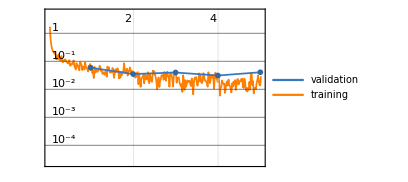
| rounds
loss | -Graphics-

```mathematica
results["LossEvolutionPlot"]
```

```mathematica
results["TrainedNet"]
```

NetGraph[<>]

将训练好的部分提取出来, 并设置入口和出口的 Layer:

```mathematica
trainedLenet=NetReplacePart[NetExtract[results["TrainedNet"],"lenet"],
{"Input"->enc,"Output"->dec}]
```

NetChain[<>]

## 训练结果和应用

随机选择几个作为例子:

```mathematica
RandomSample[testData,5]
```

{-Graphics-→5,-Graphics-→8,-Graphics-→8,-Graphics-→9,-Graphics-→9}

```mathematica
trainedLenet[Keys@%,"TopProbabilities"]
```

{{9→0.541853,5→0.453837},{8→0.999811},{8→0.98567},{9→0.999997},{9→0.999994}}

嗯识别率真的挺高的.

训练完成的网络可以用于分类.

## 保存训练结果

最后保存一下这个训练的结果, 方便以后再调用 (毕竟训练挺费时间的).

```mathematica
Export["./trained-LeNet-for-digits.wlnet",trainedLenet,"WLNet"]
```

./trained-LeNet-for-digits.wlnet

可以使用 Import 来重新导入.